```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

#### Elecrton neutrinos

```mathematica
linesEl = Import["./output/Electron neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@linesEl;
linesEl = Map[Read[StringToStream[#],Number]&, linesEl, {2}];
```

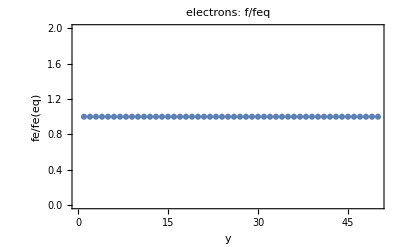

```mathematica
distEl1=Rest[linesEl[[2, All]]];
yEl=linesEl[[1,All]];
ListPlot[distEl1,PlotLabel->Style[#,Bold,15]&/@{"electrons: f/feq"},Frame-> True, FrameLabel->{"y","fe/fe(eq)"}]
```

#### Muon neutrinos

```mathematica
linesμ = Import["./output/Muon neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@linesμ;
linesμ = Map[Read[StringToStream[#],Number]&, linesμ, {2}];
```

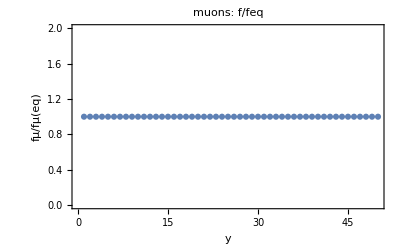

```mathematica
distμ1=Rest[linesμ[[2, All]]];
yμ=linesμ[[1,All]];
ListPlot[distμ1,PlotLabel->Style[#,Bold,15]&/@{"muons: f/feq"},Frame-> True, FrameLabel->{"y","fμ/fμ(eq)"}]
```